## Import

```mathematica
SetDirectory[NotebookDirectory[]];
pathSRC="../src/";
Get[pathSRC<>"basic.m"];
Get[pathSRC<>"dftb.m"];
Get[pathSRC<>"xyz.m"];

Get["../skf/auorg.E.m"];
Get["../skf/auorg.V.mx"];
Get["../skf/auorg.S.mx"];
```

## Ham gen

```mathematica
Main[moleName_]:=Module[{coords,types,bonds,h,s},
{coords,types,bonds}=ImportXYZ[moleName<>".xyz"];
h=DFTBSolver2[coords,types];
s=DFTBSolver2[coords,types,"S"];
Export[moleName<>".h.dat",h];
Export[moleName<>".s.dat",s];
{h,s}
]
```

```mathematica
molList={"CDAB","CNB8M6","CPP12"};
({h[#],s[#]}=Main[#])&/@molList;
```

```mathematica
h["CDAB"]⟦1;;20,1;;20⟧//MatrixForm
```

(-13.7388 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6.46409 | 3.91893 | -3.07104 | -4.71804 | -0.970429 | 0.299307 | -0.0999711 | -1.2964
0 | -5.28867 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3.91893 | 0.273996 | -2.27995 | -3.50269 | -0.299307 | -0.201282 | -0.0330899 | -0.429101
0 | 0 | -5.28867 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.07104 | -2.27995 | -0.848768 | 2.74486 | 0.0999711 | -0.0330899 | -0.289299 | 0.143323
0 | 0 | 0 | -5.28867 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.71804 | -3.50269 | 2.74486 | 1.5815 | 1.2964 | -0.429101 | 0.143323 | 1.55823
0 | 0 | 0 | 0 | -13.7388 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -5.28867 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -5.28867 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.28867 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13.7388 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.28867 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.28867 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.28867 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-6.46409 | -3.91893 | 3.07104 | 4.71804 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13.7388 | 0 | 0 | 0 | -7.63121 | -1.81509 | 2.7592 | -7.11303
3.91893 | 0.273996 | -2.27995 | -3.50269 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.28867 | 0 | 0 | 1.81509 | -2.72584 | -0.831484 | 2.14351
-3.07104 | -2.27995 | -0.848768 | 2.74486 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.28867 | 0 | -2.7592 | -0.831484 | -2.00884 | -3.25845
-4.71804 | -3.50269 | 2.74486 | 1.5815 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.28867 | 7.11303 | 2.14351 | -3.25845 | 5.12726
-0.970429 | -0.299307 | 0.0999711 | 1.2964 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -7.63121 | 1.81509 | -2.7592 | 7.11303 | -13.7388 | 0 | 0 | 0
0.299307 | -0.201282 | -0.0330899 | -0.429101 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.81509 | -2.72584 | -0.831484 | 2.14351 | 0 | -5.28867 | 0 | 0
-0.0999711 | -0.0330899 | -0.289299 | 0.143323 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.7592 | -0.831484 | -2.00884 | -3.25845 | 0 | 0 | -5.28867 | 0
-1.2964 | -0.429101 | 0.143323 | 1.55823 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -7.11303 | 2.14351 | -3.25845 | 5.12726 | 0 | 0 | 0 | -5.28867)

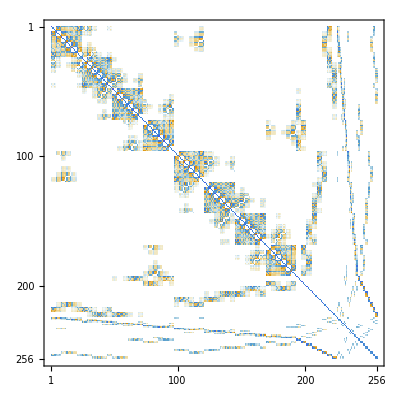

```mathematica
h["CNB8M6"]//MatrixPlot
```